## Simulated Annealing

```mathematica
SalesmanSimulatedAnnealing[cityLocations_,nSteps_]:=
Module[{currentPath,temperature,neighborPath,pathValueDifference},
currentPath=cityLocations;
Do[
temperature=CalculateTemperature[step,nSteps];
neighborPath=SalesmanNeighborSwap[currentPath];
pathValueDifference=CalculateValueDifference[neighborPath,currentPath];
If[AcceptNewPathQ[pathValueDifference,temperature],
currentPath=neighborPath
]
,{step,1,nSteps}
];
currentPath
];

CalculateTemperature[step_,nSteps_]:=
Module[{initialTemperature,decayRate},
initialTemperature=1;
decayRate=5.0;
initialTemperature*(1-(decayRate/nSteps))^step
];

CalculateValueDifference[neighborPath_,currentPath_]:=
SalesmanTourDistance[neighborPath]-SalesmanTourDistance[currentPath];

AcceptNewPathQ[pathValueDifference_,temperature_]:=
Module[{probAccept},
probAccept=E^(-pathValueDifference/temperature);
RandomReal[]<probAccept
];

SalesmanTourDistance[cityPath_]:=Module[{totalLength},
totalLength=0;
Do[
totalLength=totalLength+EuclideanDistance[cityPath[[i]],cityPath[[i+1]]]
,{i,1,Length[cityPath]-1}
];
totalLength=totalLength+EuclideanDistance[cityPath[[1]],cityPath[[-1]]];
totalLength
];

SalesmanNeighborSwap[currentPath_]:=
Module[{newPath,swapIndices},
newPath=currentPath;
swapIndices=RandomSample[Range[Length[currentPath]],2];
newPath[[swapIndices]]=newPath[[Reverse[swapIndices]]];
newPath
]
```

## Watch it run

```mathematica
SalesmanSimulatedAnnealingStep[currentPath_,temperature_]:=
Module[{neighborPath,pathValueDifference},
neighborPath=SalesmanNeighborSwap[currentPath];
pathValueDifference=CalculateValueDifference[neighborPath,currentPath];
If[AcceptNewPathQ[pathValueDifference,temperature],
neighborPath,
currentPath
]
];
```

```mathematica
nCities=50;
cityLocations=RandomReal[{0,1},{nCities,2}];
nSteps=100000;
```

```mathematica
Dynamic[outputGraph]
currentPath=cityLocations;
Do[
temperature=CalculateTemperature[step,nSteps];
currentPath=SalesmanSimulatedAnnealingStep[currentPath,temperature];
If[Mod[step,100]==0,
outputGraph=ListLinePlot[
currentPath,
Mesh->Full,
MeshStyle->Opacity[0.2],
PlotLabel->"Iteration: "<>ToString[step]<>
"\nTotal Distance: "<>ToString[SalesmanTourDistance[currentPath]]<>
"\nTemperature: "<>ToString[temperature]
]
];
,{step,1,nSteps}
];
```

```mathematica
(*Use a specialized algorithm built-in with Mathematica*)
```

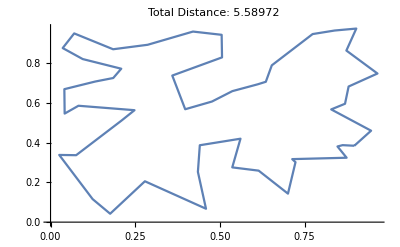

-Graphics-

```mathematica
{optPathLength, optPathOrder} = FindShortestTour[cityLocations];
ListLinePlot[cityLocations[[optPathOrder]],PlotLabel->"Total Distance: "<>ToString[optPathLength]]
```